```mathematica
ClearAll["Global'*"]

eq1=x*(y-1)-0.2
eq2=(1+1.2*y-2*x)*y
eqps=Solve[{eq1==0,eq2==0},{x,y}]
```

-0.2+x (-1+y)

y (1-2 x+1.2 y)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.2,y→0.},{x→-0.1,y→-1.},{x→1.2,y→1.16667}}

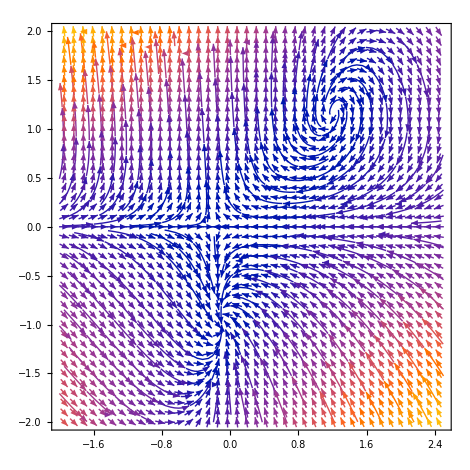

```mathematica
vf=StreamPlot[{eq1,eq2},{x,-2,2.5},{y,-2,2},VectorPoints->40, VectorScale->{0.02,1.5,None}, VectorStyle->Gray]
```

{-0.2,0.}

{-0.1,-1.}

{1.2,1.16667}

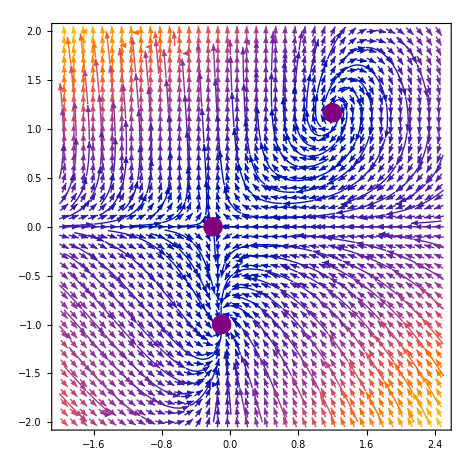

```mathematica
X1=x/.eqps[[1]]; Y1=y/.eqps[[1]];   
eqp1={X1,Y1}
X2=x/.eqps[[2]]; Y2=y/.eqps[[2]];  
eqp2={X2,Y2}
X3=x/.eqps[[3]]; Y3=y/.eqps[[3]];
eqp3={X3,Y3}
ploteqp=ListPlot[{eqp1,eqp2,eqp3},PlotStyle->{PointSize[0.03],Purple}];
Show[vf,ploteqp]
```

```mathematica
eqps
Deq1x=y-1
Deq1y=-2x
Deq2x=-2*y
Deq2=-2*x

A={{y-1,x},{-2y,-2*x}}

B={{y-1,x},{-2y,-2*x}}

G={{y-1,x},{-2y,-2*x}}

MatrixForm[Limit[A,{x,y}->{X1,Y1}]]
MatrixForm[Limit[B,{x,y}->{X2,Y2}]]
MatrixForm[Limit[G,{x,y}->{X3,Y3}]]
```

{{x→-0.2,y→0.},{x→-0.1,y→-1.},{x→1.2,y→1.16667}}

-1+y

-2 x

-2 y

-2 x

{{-1+y,x},{-2 y,-2 x}}

{{-1+y,x},{-2 y,-2 x}}

{{-1+y,x},{-2 y,-2 x}}

(-1. | -0.2
0. | 0.4)

(-2. | -0.1
2. | 0.2)

(0.166667 | 1.2
-2.33333 | -2.4)

```mathematica
Eigenvalues[Limit[A,{x,y}->{X1,Y1}]]
```

{-1.,0.4}

```mathematica
Eigenvectors[Limit[A,{x,y}->{X1,Y1}]]
```

{{1.,0.},{-0.141421,0.989949}}

```mathematica
Eigenvalues[Limit[B,{x,y}->{X2,Y2}]]
```

{-1.90499,0.104988}

```mathematica
Eigenvectors[Limit[B,{x,y}->{X2,Y2}]]
```

{{-0.724954,0.688797},{0.0474527,-0.998873}}

```mathematica
Eigenvalues[Limit[G,{x,y}->{X3,Y3}]]
Eigenvectors[Limit[G,{x,y}->{X3,Y3}]]
```

{-1.11667+1.0738 ⅈ,-1.11667-1.0738 ⅈ}

{{-0.44695-0.373977 ⅈ,0.812636+0. ⅈ},{-0.44695+0.373977 ⅈ,0.812636+0. ⅈ}}

```mathematica
ClearAll["Global'*"]
```

```mathematica
----------------------------------------------
```

```mathematica
deq1=x'[t]==x[t]*(y[t]-1)-0.2
deq2=y'[t]==(1+1.2*y[t]-2*x[t])*y[t]
```

x'[t]==-0.2+x[t] (-1+y[t])

y'[t]==y[t] (1-2 x[t]+1.2 y[t])

```mathematica
XS1=-0.2;
YS1=0;
```

```mathematica
XS2=-0.1;
YS2=-1;
```

```mathematica
XS3=1.2;
YS3=1.166667;
```

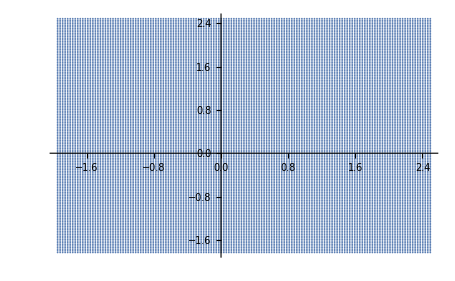

```mathematica
arxikes=Table[{x0,y0},{x0,-2+0.0532,2.5,0.03},{y0,-2+0.166,2.5,0.03}];
arxikes=Flatten[arxikes,1];
ListPlot[arxikes]
```

```mathematica
n=Length[arxikes]
```

21605

```mathematica
per1={{XS1,YS1}};
```

```mathematica
per2={{XS2,YS2}};
```

```mathematica
per3={{XS3,YS3}};
```

```mathematica
per4={};
```

```mathematica
tmax=45;
For[i=1,i<=n,i++,
x0=arxikes[[i,1]]; y0=arxikes[[i,2]];
sol=NDSolve[{deq1,deq2,x[0]==x0,y[0]==y0},{x,y},{t,0,tmax,20},Method->"StiffnessSwitching"];
xt=x/.sol[[1]]; yt=y/.sol[[1]];
Xf=xt[tmax]; Yf=yt[tmax];
d1=Sqrt[(Xf-XS1)^2+(Yf-YS1)^2];
d2=Sqrt[(Xf-XS2)^2+(Yf-YS2)^2];
d3=Sqrt[(Xf-XS3)^2+(Yf-YS3)^2];
Which[d1<0.005,AppendTo[per1,{x0,y0}],d2<0.005, AppendTo[per2,{x0,y0}],d3<0.005,AppendTo[per3,{x0,y0}],True,AppendTo[per4,{x0,y0}]]]
Short[per1];
Short[per2];
Short[per3];
```

NDSolve::ndsz: At t == 1.24221, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {45} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 0.986504, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {45} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.857985, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

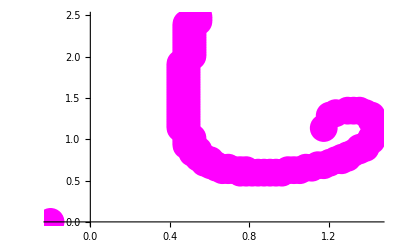

```mathematica
set1=ListPlot[per1,PlotStyle->{RGBColor[5,0,5],PointSize[0.05]}]
```

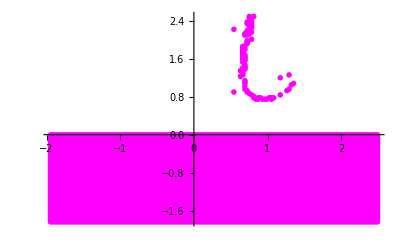

```mathematica
set2=ListPlot[per2,PlotStyle->{RGBColor[2,0,7],PointSize[0.01]}]
```

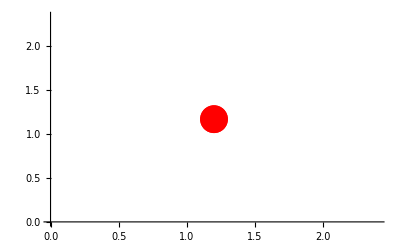

```mathematica
set3=ListPlot[per3,PlotStyle->{Red,PointSize[0.05]},PlotRange->Full]
```

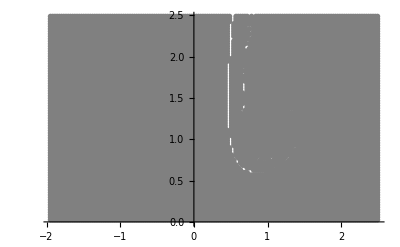

```mathematica
set4=ListPlot[per4,PlotStyle->{Gray,PointSize[0.01]}]
```

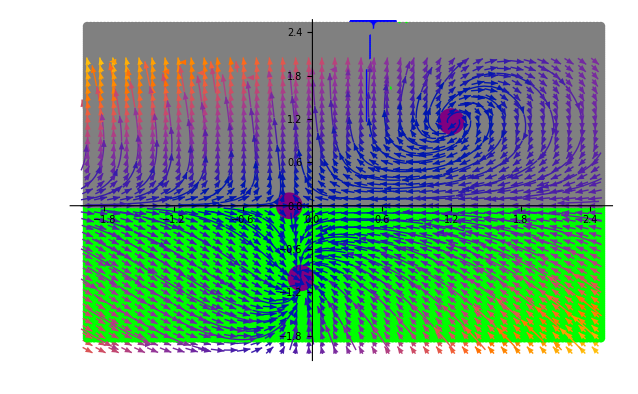

```mathematica
Show[{set1,set2,set3,set4,ploteqp,vf},PlotRange->Full]
```